```mathematica
Needs["Dodelson`TESTCommonParameters`"]
equalitySubs
ayetaSubs
EnergyDenSubs
SoundSubs
```

SubscriptSymbols::list: The subscript specification list given to SubscriptSymbols must be a list of variables, or a list of subscripted variables. They can't be mixed.

Needs::nocont: Context TraditionalForm`"Dodelson`TESTCommonParameters`" was not created when Needs was evaluated.

Some definitions referencing 'equality' point :

defkeq :: k_eq→a_eq H(a_eq)

subkeq :: k_eq→√2 √((H_0^2 Ω_m)/a_eq)

subH0 :: H_0→(√((a_eq k_eq^2)/Ω_m))/(√2)

subkkeq :: k→k_eq kk_eq

subetat :: η'(t)→1/(a(η))

subyeta :: y(η)→(a(η))/a_eq

subDyeta :: y'(η)→(a'(η))/a_eq

subHt :: H→(a'(t))/(a(t))

defaeta :: a(η_):=y(η) a_eq

subHeta :: H→(a'(η))/(a(η))^2

deffnu :: f_ν:=ρ_ν/(ρ_γ+ρ_ν)

defRhoG :: ρ_γ(a_):=(C_γ (1/a)^4 ρ_cr)/h^2

defRhoRad :: ρ_r(a_):=(ρ_γ(a))/(1-f_ν)

defRhoB :: ρ_b(a_):=(Ω_b ρ_cr)/a^3

defRhoM :: ρ_m(a_):=(Ω_m ρ_cr)/a^3

defRhoDE :: ρ_de(a_):=(Ω_de ρ_cr)/a^3

defRho :: ρ(a_):=ρ_de(a)+ρ_m(a)+ρ_r(a)

defOmegaM :: Ω_m:=Ω_b+Ω_dm

subRhoCR :: ρ_cr→(3 H_0^2)/(8 G π)

defe255 :: (∂ρ_t(t))/(∂t)+(3 (∂a_t(t))/(∂t) (𝒫_t(t)+ρ_t(t)))/(a_t(t))==0

defe255a :: (∂ρ_a(a))/(∂a)+(3 (𝒫_a(a)+ρ_a(a)))/a==0

subaeq :: a_eq→-C_γ/((f_ν-1) h^2 Ω_m)

subC :: C_γ→-a_eq (f_ν-1) h^2 Ω_m

defHa :: Ha(a_):=√(1/3 (8 π G) ρ(a))

defetade :: η_de(a_):=∫_0^a 1/(aa^2 Ha(aa))ⅆaa

defe242 :: χ(a_):=∫_a^1 1/(aa^2 Ha(aa))ⅆaa

For backward consistency : Null

η[a_] :: (2 (√(a+a_eq)-√a_eq))/(H_0 √Ω_m)

η_* :: (2 (√(a_eq+a_Times)-√a_eq))/(H_0 √Ω_m)

η_y[y_] :: (2 (√(y a_eq+a_eq)-√a_eq))/(H_0 √Ω_m)

Jacobian dη/dy => a_eq/(H_0 √(a_eq (y+1)) √Ω_m)
Or  -> dη/dy = (√2)/(k_eq √(y+1))

y[η_] :: 1/8 k_eq η (k_eq η+4 √2)

Useful relationships: From the definitions: dη==dt/a  and  H=((∂a(t))/(∂t))/(a(t)) => a H==(∂a(t))/(∂t) => dt==da/(a H) => dη==da/(a^2 H)

defR :: R(a_):=(3 ρ_b(a))/(4 ρ_γ(a))

defReta :: R_η(η_):=(3 ρ_b(y(η) a_eq))/(4 ρ_γ(y(η) a_eq))

Eqn819 :: c_s(a_):=√(1/(3 (R(a)+1)))

Eqn819eta :: c_s(eta_):=√(1/(3 (R_η(eta)+1)))

Eqn822 :: r_s(η_):=∫_0^η c_s(ep)ⅆep

c_s(eta_):=√(1/(3 (R_η(eta)+1))) => 1/(√3 √(1-(3 k_eq η (k_eq η+4 √2) Ω_b)/(32 (f_ν-1) Ω_m)))Null

r_s[η_] :: -1/(3 k_eq f_b^(1/2))4 √2 √(1-f_ν) (log((4 √6 f_b^(1/2))/(√(1-f_ν))-(6 √2 f_b)/(f_ν-1))-log((√3 f_b^(1/2) √(32-(3 k_eq η (k_eq η+4 √2) f_b)/(f_ν-1)))/(√(1-f_ν))-(3 (k_eq η+2 √2) f_b)/(f_ν-1)))

We compute the sound horizon, r_s[η] to be :  r_s[η]= -1/(3 k_eq f_b^(1/2))4 √2 √(1-f_ν) (log((4 √6 f_b^(1/2))/(√(1-f_ν))-(6 √2 f_b)/(f_ν-1))-log((√3 f_b^(1/2) √(32-(3 k_eq η (k_eq η+4 √2) f_b)/(f_ν-1)))/(√(1-f_ν))-(3 (k_eq η+2 √2) f_b)/(f_ν-1)))
where 
f_b->Ω_b/Ω_m, the baryon-to-total-matter energy fraction
f_ν->ρ_ν/ρ_ν, the neutrino-to-total-radiation energy fraction
k_eq->a_eqH[a_eq], the rate of change of the scale factor at matter-radiation equality
η->conformal time

We use this r_s[η_*] to plot corresponding values to HS Fig.5.

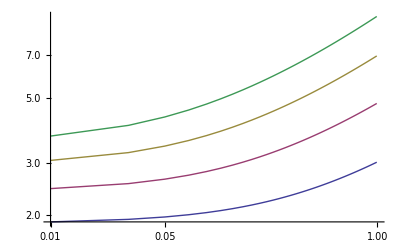

This similar to Hu-Sugiyama Fig.5.
Here we use Ω_0->Ω_m+(Ω_γ+Ω_ν)/h^2->1.

```mathematica
Print["We compute the sound horizon, r_s[η] to be :  r_s[η]= ",Subscript[r, s][η],"
where 
f_b->Ω_b/Ω_m, the baryon-to-total-matter energy fraction
f_ν->ρ_ν/ρ_ν, the neutrino-to-total-radiation energy fraction
k_eq->a_eqH[a_eq], the rate of change of the scale factor at matter-radiation equality
η->conformal time
"];
Print["
We use this r_s[η_*] to plot corresponding values to HS Fig.5."];
Subscript[r, s][SubStar[η]] sec2Mpc/.Subscript[f, b]->(Subscript[Ω, b]/Subscript[Ω, m])//NumericalValues;
rsstar=%/.Subscript[Ω, m]->(1-Subscript[C, γ]/(h^2(1-Subscript[f, ν])))//NumericalValues//Simplify;

Table[
{  OO,100 π/(rsstar/.Subscript[Ω, b]->OO/.h->HH//PowerExpand)   }
,{HH,.4,1,.2}
,{OO,.01,1,.02}
];
ListLogLogPlot[ %,Joined->True]
Print["This similar to Hu-Sugiyama Fig.5.
Here we use Ω_0->Ω_m+(Ω_γ+Ω_ν)/h^2->1."]
```